```mathematica
Clear["Global`*"]
```

```mathematica
(*把HH模型降维到二维,FitzHugh-Nagumo model*)
```

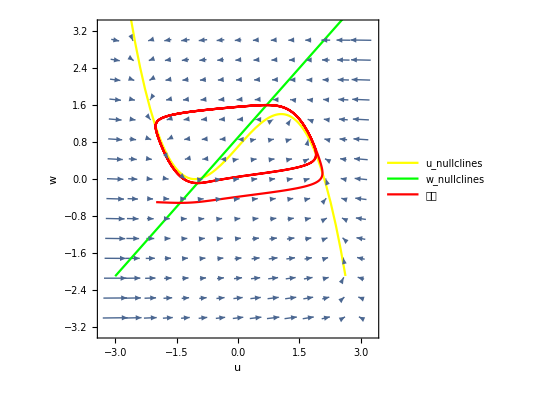

C:\Users\quanzai\Desktop\Neuronal-Dynamics\Chapter1\降维到二维\Is=0FN相图.pdf

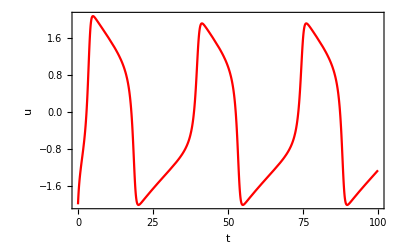

C:\Users\quanzai\Desktop\Neuronal-Dynamics\Chapter1\降维到二维\Is=0FN电压.pdf

```mathematica
Is=0.7;
ϵ=0.1;
b0=0.9;
b1=1; 
λ=0.3;
du=u-λ*u^3-w+Is;
dw=ϵ*(b0+b1*u-w);
linew=b0+b1*u;
lineu=u-λ*u^3+Is;
vp=VectorPlot[{du,dw},{u,-3, 3}, {w, -3, 3}];
up=Plot[lineu,{u,-3,3},PlotStyle->{Yellow},PlotLegends->{"u_nullclines"}];
wp=Plot[linew,{u,-3,3},PlotStyle->{Green},PlotLegends->{w_nullclines}];
sol=NDSolve[{u'[t]==u[t]-λ*u[t]^3-w[t]+Is,w'[t]==ϵ*(b0+b1*u[t]-w[t]),u[0]==-2,w[0]==-0.5},{u,w},{t,0,100}];
pp=ParametricPlot[{u[t],w[t]}/.First@sol//Evaluate,{t,0,100},PlotRange->All,PerformanceGoal->"Quality",PlotStyle->{Red},PlotLegends->{"轨迹"}];
ans=Show[{vp,up,wp,pp},Frame->True,FrameLabel->{"u","w"},LabelStyle->{FontFamily->"Times New Roman"}]
Export["C:\\Users\\quanzai\\Desktop\\Neuronal-Dynamics\\Chapter1\\降维到二维\\Is=0FN相图.pdf",ans]
sol=NDSolve[{u'[t]==u[t]-λ*u[t]^3-w[t]+Is,w'[t]==ϵ*(b0+b1*u[t]-w[t]),u[0]==-2,w[0]==-0.5},u,{t,0,100}];
ans=Plot[u[t]/.sol,{t,0,100},PlotRange->All,PlotStyle->{Red},LabelStyle->{FontFamily->"Times New Roman"},Frame->True,FrameLabel->{"t","u"}]
Export["C:\\Users\\quanzai\\Desktop\\Neuronal-Dynamics\\Chapter1\\降维到二维\\Is=0FN电压.pdf",ans]
```